```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools}"}];
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

```mathematica
$K = 9;
```

```mathematica
plotsDir = "../../plots/plots-101";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
Do[data[k] = {}, {k, 2, 1+$K($K+1)}];
Do[Module[{}, (
d = Import["../../runs/Stats-101/N"<>ToString@$N<>"K"<>ToString@$K<>".dat"];
Do[AppendTo[data[k], {$N, Around[d[[All, k]]]}], {k, 2, 3}];
Do[AppendTo[data[k], {$N, Around[d[[All, k]]]}], {k, 4, 1+$K($K+1), 1}];
)], {$N, 3, 8}]
```

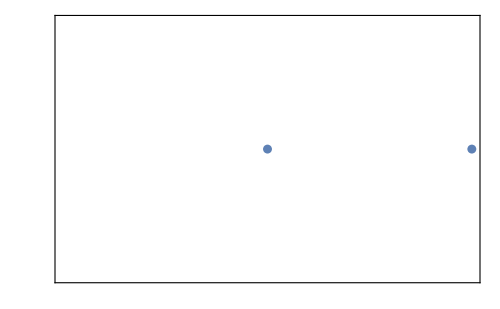

```mathematica
(* Mean of TrX^2 *)
plt1 = ListPlot[{1,1},
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
FrameLabel->MaTeX/@{"N", "\\expval{\\Tr X^2}_t"},
FrameTicks->{{With[{ticks=1.5+0.2Range[0,10]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,9]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
ImageSize->500
]
```

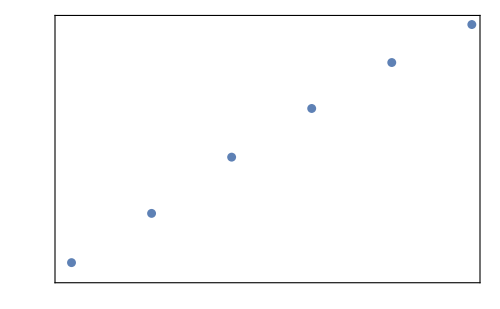

```mathematica
Export[plotsDir<>"/monopole-mean.pdf", plt1, ImageResolution->300];
plt1
```

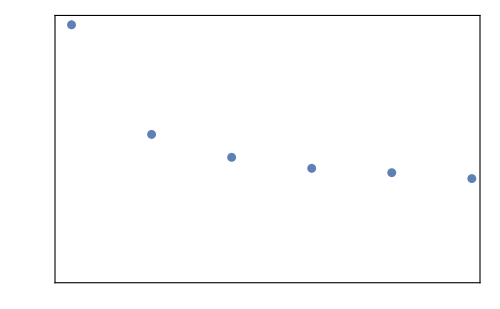

```mathematica
(* SD of TrX^2 *)
plt2 = ListPlot[data[3],
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotRange->All,
FrameLabel->MaTeX/@{"N", "\\sigma(\\Tr X^2)_t"},
FrameTicks->{{With[{ticks=0.0+0.05Range[0,20]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,20]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
ImageSize->500
];
Export[plotsDir<>"/monopole-sd.pdf", plt2, ImageResolution->300];
plt2
```

```mathematica
latexExp[i_, j_] := Module[{}, (
If[i == j, 
"\\frac{8}{"<>ToString@$K<>"}\\Tr (X^{"<>ToString@i<>"})^2"<>" - \\frac{1}{"<>ToString@$K<>"}\\sum_{i=2}^{9} \\Tr(X^{i})^2 "
(*StringJoin@Table[If[k==i, Nothing, " - \\frac{1}{"<>ToString@$K<>"} \\Tr (X^{"<>ToString@k<>"})^2"], {k, 1, $K}]*),
"\\Tr X^{"<>ToString@i<>"} X^{"<>ToString@j<>"}"
]
)];
```

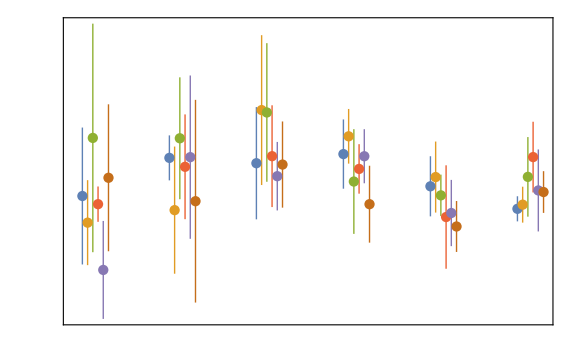

```mathematica
(* Mean of SymTr *)
plt3 = ListPlot[Table[Table[{data[k][[A, 1]]+0.03(k-9), data[k][[A, 2]]}, {A, 1, Length[data[k]]}], {k, 4, 14, 2}],
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
FrameLabel->MaTeX/@{"N", "\\expval{\\Tr X^i X^j - \\frac{\\delta^{i j}}{K} \\Tr X^2}_t"},
FrameTicks->{{With[{ticks=-0.08+0.02Range[0,10]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,9]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
PlotRange->All,
PlotLegends->MaTeX/@(Flatten@Table[latexExp[i, j], {i, 1, $K-1}, {j, i, $K}]),
ImageSize->Large
];
Export[plotsDir<>"/quadrupole-mean.pdf", Rasterize[plt3, ImageResolution->300]];
plt3
```

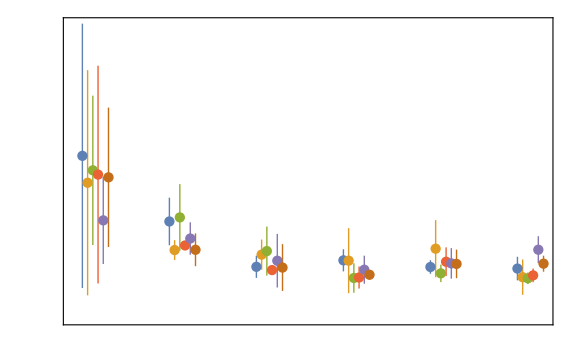

```mathematica
(* SD of SymTr *)
plt4 = ListPlot[Table[Table[{data[k][[A, 1]]+0.03(k-10), data[k][[A, 2]]}, {A, 1, Length[data[k]]}], {k, 5, 15, 2}],
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
FrameLabel->MaTeX/@{"N", "\\sigma(\\Tr X^i X^j - \\frac{\\delta^{i j}}{K} \\Tr X^2)_t"},
FrameTicks->{{With[{ticks=0+0.05Range[0,10]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=Range[2,9]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
PlotLegends->MaTeX/@(Flatten@Table[latexExp[i, j], {i, 1, $K-1}, {j, i, $K}]),
PlotRange->All,
ImageSize->Large
];
Export[plotsDir<>"/quadrupole-sd.pdf", Rasterize[plt4, ImageResolution->300, ImageSize->Large]];
plt4
```